Grid

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
pts={};
nPts=11;
Do[
Do[
AppendTo[pts,{(i-1)/10.0,(j-1)/10.0}];
,{j,1,nPts}];
,{i,1,nPts}];
```

```mathematica
f=OpenWrite["grid.txt"];
Do[
s=ToString[pt[[1]]]<>" "<>ToString[pt[[2]]];
WriteLine[f,s];
,{pt,pts}];
Close[f];
```

Data

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data={};
radius=0.3;
nData=20;
Do[
x=0.5+radius*Cos[2*Pi*(i-1)/(nData-1)];
y=0.5+radius*Sin[2*Pi*(i-1)/(nData-1)];
If[i≠nData,
z=RandomReal[{0,1}],
z=data[[1,3]]
];
AppendTo[data,{x,y,z}];
,{i,1,nData}];
```

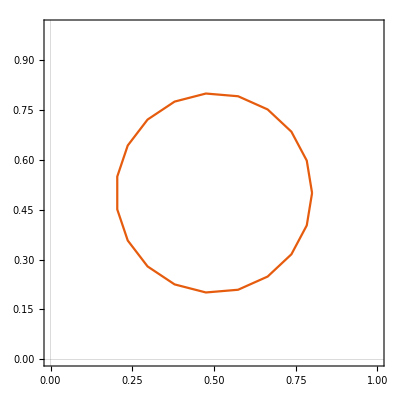

```mathematica
ListLinePlot[data[[;;,{1,2}]],AspectRatio->1,PlotRange->{{0,1},{0,1}}]
```

```mathematica
ListPointPlot3D[data,PlotRange->{{0,1},{0,1},{0,1}}]/.Point->Line
```

-Graphics3D-

```mathematica
f=OpenWrite["path.txt"];
Do[
s=ToString[pt[[1]]]<>" "<>ToString[pt[[2]]]<>" "<>ToString[pt[[3]]];
WriteLine[f,s];
,{pt,data}];
Close[f];
```